# Lista 04 - Introdução à Física Computacional I

Lyliana Myllena Santos de Sousa - 11223740
Lyliana.sousa@usp.br

Ao preparar o Notebook da lista, faça uso abundante de comentários e textos explicativos. Não se esqueça de rotular devidamente os eixos dos gráficos que produzir.

## 1.

O telescópio espacial James Webb, que deve ser lançado em breve, orbitará o Sol em um dos chamados pontos de Lagrange, em que um objeto permanece em repouso em relação à Terra. Ao longo deste problema, vamos investigar esses pontos em um contexto mais geral, envolvendo dois corpos celestes de massas M_1 e M_2 que descrevem trajetórias circulares em torno de seu centro de massa. Para a descrição do movimento desses corpos e de “corpo de teste”, de massa 𝓂 desprezível frente a M_1 e M_2, é conveniente adotar um referencial que gira juntamente com os dois maiores corpos, com a mesma velocidade angular ω destes. Vamos supor que, nesse referencial, o movimento ocorra no plano 𝓍𝓎, e vamos adotar o eixo 𝓍 como aquele em que se situam os centros de M_1 e M_2. Podemos então escrever os vetores posição dessas massas respectivamente como (r⃗)_1=(x_1, y_1) e (r⃗)_2=(x_2, y_2), com y_1 = y_2 = 0, x_1 = - (M_2 R)/(M_1  + M_2) e x_2 =  (M_1 R)/(M_1  + M_2), sendo R a distância entre as massas. Como o referencial que adotamos não é inercial, a descrição do movimento requer a introdução de forças fictícias, de modo que a dependência da força resultante efetiva sobre o corpo com sua posição r⃗  é obtida do potencial efetivo: V(r⃗) = - (G M_1)/(|r⃗ - (r⃗)_1|) - (G M_2)/(|r⃗ - (r⃗)_2|) - 1/2 ω^2(|r⃗|)^2 , sendo ω^2 = G (M_1 + M_2)/R^3.

• Medindo comprimentos em unidades de R, massas em unidades de M_1 e o potencial em unidades de G M_1/R, e supondo M_2 = M_1/4,  trace um gráfico de curvas de nível de V (r⃗) que mostre os 5 pontos de Lagrange, três dos quais situam-se no eixo 𝓍 (dois próximos de M_2 e um do lado oposto em relação a  M_1 ), com os dois outros pontos tendo 𝓎 ≠ 0. Procure ajustar os intervalos de 𝓍 e 𝓎, bem como a escala do potencial e o número de curvas de nível, para indicar claramente a existência esses pontos.

(Resposta) Plotarei as curvas de níveis usando a função CountourPlot nos pontos de Lagrange, que consiste nos pontos críticos, ou seja, os pontos onde o gradiente da função é nulo.  Utilizando coordenadas cartesianas e as informações do enunciado teremos o nosso potencial efetivo descrito pela seguinte expressão:
V(r⃗) = V(x,y)  = - 1/(√((x + (M_2 R)/(M_1  + M_2))^2+ y^2)) -1/4*1/(√((x - (M_1 R)/(M_1  + M_2))^2+ y^2))  - 5/8*(x^2+ y^2  )             [(G M_1)/R]

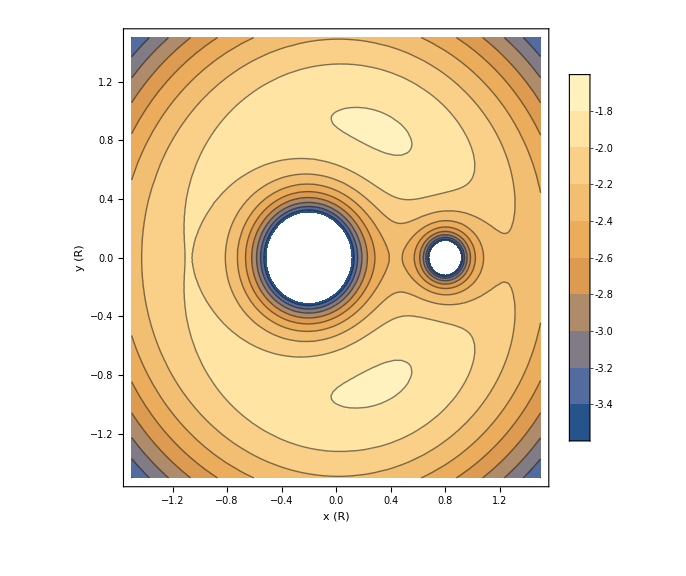

```mathematica
v[x_,y_]:= - (G* Subscript[M, 1])/(√((x +(Subscript[M, 2] R)/(Subscript[M, 1]  + Subscript[M, 2]))^2+ y^2)) - (G* Subscript[M, 2])/(√((x - (Subscript[M, 1] R)/(Subscript[M, 1]  + Subscript[M, 2]))^2+ y^2)) - 1/2*ω^2*(x^2+ y^2)/.{G-> 1, R-> 1,Subscript[M, 1]-> 1, Subscript[M, 2]-> 1/4, ω-> √(5/4)}
optam={ImageSize-> Large,LabelStyle-> Large};
ContourPlot[v[x,y],{x,-1.5,1.5},{y,-1.5,1.5},Evaluate[optam],FrameLabel->{"x (R)","y (R)","V (G M_1/R)"},PlotLegends->Automatic]
```

Abaixo podemos ver as regiões dos pontos de Lagrange destacadas:
-Graphics-

De acordo com a referencia [http://wray.eas.gatech.edu/physicsplanets2014/LectureNotes/LagrangePointDerivation_MontanaStateU.pdf], as coordenadas dos pontos de Lagrange são dados por: 
L_1:(R[1 - (M_2/(3(M_1  + M_2)))^(1/3)],0) 
L_2: (R[1 + (M_2/(3(M_1  + M_2)))^(1/3)],0)
L_3:(-R[1  + (5 M_2)/(12(M_1  + M_2))],0)
L_4:(R/2((M_1 - M_2)/(M_1  + M_2)),(√3)/2 R)
L_5: (R/2((M_1 - M_2)/(M_1  + M_2)),-(√3)/2R)

```mathematica
l1 =N[ v[R(1 - (Subscript[M, 2]/(3*(Subscript[M, 1]  + Subscript[M, 2])))^(1/3)),0]];
l2 =N[v[R(1 + (Subscript[M, 2]/(3*(Subscript[M, 1]  + Subscript[M, 2])))^(1/3)),0]];
l3 = N[v[-R(1  + (5 Subscript[M, 2])/(12*(Subscript[M, 1]  + Subscript[M, 2]))),0]];
l4 =N[  v[R/2((Subscript[M, 1] - Subscript[M, 2])/(Subscript[M, 1]  + Subscript[M, 2])),(√3)/2 R]];
l5 = N[v[R/2((Subscript[M, 1] - Subscript[M, 2])/(Subscript[M, 1]  + Subscript[M, 2])),-(√3)/2 R]];
```

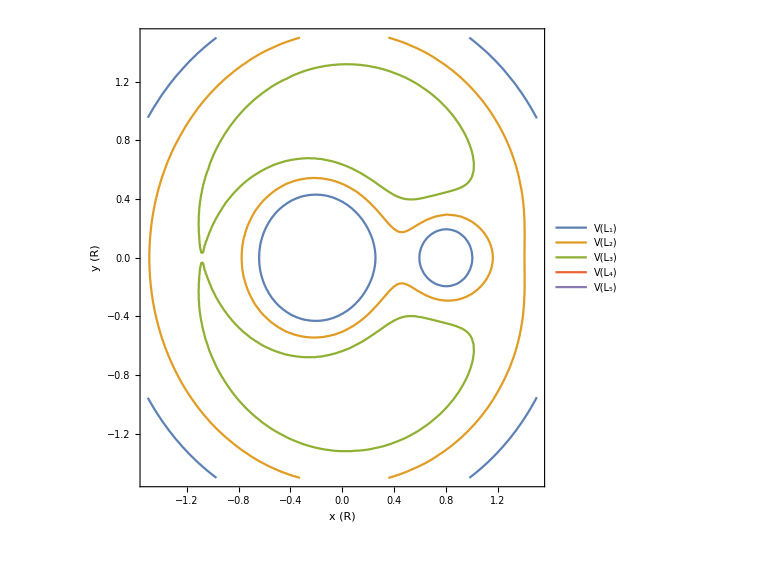

```mathematica
ContourPlot[{v[x,y]==l1,v[x,y]==l2,v[x,y]==l3,v[x,y]==l4,v[x,y]== l5},{x,-1.5,1.5},{y,-1.5,1.5},Evaluate[optam],FrameLabel->{"x (R)","y (R)","V (G M_1/R)"},PlotLegends->{"V(L_1)","V(L_2)","V(L_3)","V(L_4)","V(L_5)"}]
```

• Esses pontos caracterizam-se pelo fato de que neles a força efetiva, proporcional ao gradiente de V (r⃗), é nula. Determine numericamente as posições dos 5 pontos, ainda para o caso M_2 = M_1/4.

(Resposta) Dizer que nos pontos de lagrange o gradiente do potencial efetivo é nulo,equivale à: ∇ V⃗(r⃗) = OverVector[0] ⟶ |∇ V⃗(r⃗) |^2= 0

```mathematica
mv = Grad[v[x,y],{x,y}].Grad[v[x,y],{x,y}];
pontoslagrange =NSolve[mv== 0,{x,y}]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(121001 x)/175984-(92291 y)/87992 == 1.

{{x→0.137607-0.918329 ⅈ,y→-1.04363+0.602002 ⅈ},{x→0.137607+0.918329 ⅈ,y→-1.04363-0.602002 ⅈ},{x→-1.04502-0.0196832 ⅈ,y→-0.268365+0.0129032 ⅈ},{x→-1.04502+0.0196832 ⅈ,y→-0.268365-0.0129032 ⅈ},{x→-0.00449768-0.0443663 ⅈ,y→-0.950471+0.0290839 ⅈ},{x→-0.00449768+0.0443663 ⅈ,y→-0.950471-0.0290839 ⅈ}}

• Escolha agora M_2 = 3*10^-6 M_1,  correspondente à situação da Terra em relação ao Sol, e procure encontrar as posições dos dois pontos de Lagrange próximos à Terra. Com base nessa solução e no valor da distância entre a Terra e o Sol, determine a distância a que o James Webb estará da Terra quando estiver funcionando. (O equilíbrio nesses pontos de Lagrange próximos à Terra é instável, de modo que o telescópio precisará ser reposicionado periodicamente.)

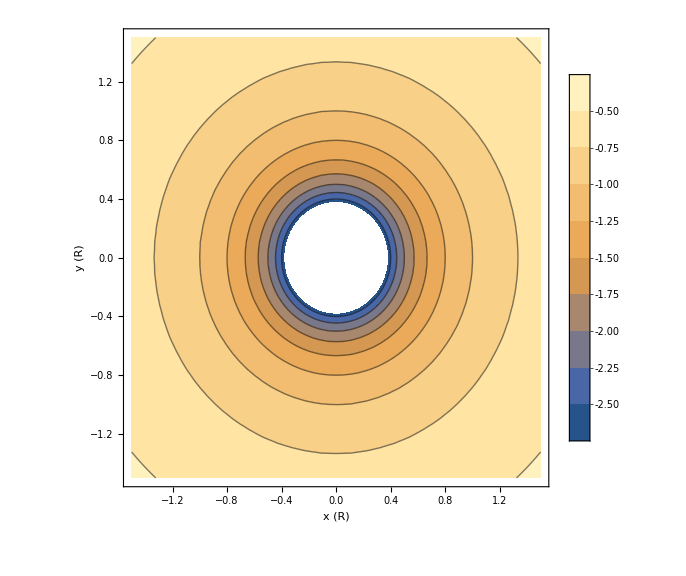

```mathematica
vsol[x_,y_]:= - (G* Subscript[M, 1])/(√((x +(Subscript[M, 2] R)/(Subscript[M, 1]  + Subscript[M, 2]))^2+ y^2)) - (G* Subscript[M, 2])/(√((x - (Subscript[M, 1] R)/(Subscript[M, 1]  + Subscript[M, 2]))^2+ y^2)) - 1/2*ω^2*(x^2+ y^2)/.{G-> 1, R-> 1,Subscript[M, 1]-> 1, Subscript[M, 2]->  3*10^-6, ω-> √(3*10^-6)}
ContourPlot[vsol[x,y],{x,-1.5,1.5},{y,-1.5,1.5},Evaluate[optam],FrameLabel->{"x (R)","y (R)","V (G M_1/R)"},PlotLegends->Automatic]
```

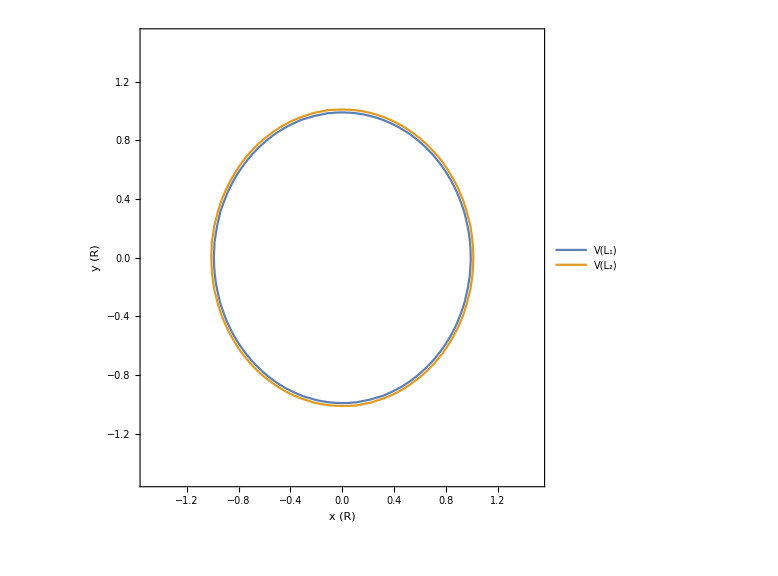

```mathematica
Clear[l1,l2]
l1 =N[ vsol[R(1 - (Subscript[M, 2]/(3*(Subscript[M, 1]  + Subscript[M, 2])))^(1/3)),0]];
l2 =N[vsol[R(1 + (Subscript[M, 2]/(3*(Subscript[M, 1]  + Subscript[M, 2])))^(1/3)),0]];
ContourPlot[{vsol[x,y]==l1,vsol[x,y]==l2},{x,-1.5,1.5},{y,-1.5,1.5},Evaluate[optam],FrameLabel->{"x (R)","y (R)","V (G M_1/R)"},PlotLegends->{"V(L_1) " ,"V(L_2) "}]
```

## 2.

Um dipolo elétrico posicionado na origem e oscilando na direção 𝓏produz radiação eletromagnética (veja Griffiths, Introduction to Electrodynamics). O campo elétrico correspondente na posição r⃗ e no instante 𝓉 é dado por: E⃗ = -A/rSin[θ]Cos[ω(t - r/c)]θ̂, sendo r = |r⃗|, A uma constante, ω a frequência angular de oscilação do dipolo, c a velocidade da luz, θ o ângulo com o eixo +z, θ̂ o vetor unitário: θ̂ = Cos[θ]Cos[ϕ]x̂ +  Cos[θ]Sin[ϕ]ŷ -  Sin[θ]ẑ e ϕ o ângulo azimutal das coordenas esféricas.

• Crie uma animação do padrão do módulo do campo elétrico no plano 𝓎𝓏, correspondente a x = 0, ou seja, ϕ = π/2. Você pode escolher unidades em que  A = c = ω = 1. A animação deve conter 24 quadros por período do movimento, com cada quadro correspondendo a uma gráfico de densidade produzido a partir do módulo do campo elétrico. Utilize um intervalo fixo de valores do módulo do campo elétrico para todos os quadros, e escolha uma número de pontos em cada quadro que produza padrões suaves. Para servir de guia, eis o quadro correspondente a t = 0:
-Graphics-

(Resposta) Para criar a animação, primeiro vou definir a função módulo do campo elétrico, convertendo coordenadas polares para as coordenadas cartesianas do plano yz, onde :r = |r⃗| = √(y^2 + z^2) e θ = Cos^-1(z/(√(y^2 + z^2))). Assim, o módulo do campo elétrico  será dado por: 
|E⃗ (r, θ,t)|= |A/r Sin[θ]Cos[ω(t - r/c)]| ⟶ |E⃗ (y,z,t)|= |A/(√(y^2 + z^2))Sin[ Cos^-1(z/(√(y^2 + z^2)))]Cos[ω(t - √(y^2 + z^2)/c)]|  
Utilizando A = c = 1 e com uma pequena alteração do que foi dito no enunciado e considerando ω  = 2π. Temos:
 |E⃗ (y,z,t)|= |1/(√(y^2 + z^2))Sin[ Cos^-1(z/(√(y^2 + z^2)))]Cos[ω(t - √(y^2 + z^2))]|  . Com isso, utilizarei a função DensityPlot para observar o comportamento do campo elétrico. Abaixo, temos um teste, mostrando que chegamos em um resultado parecido com o do professor.

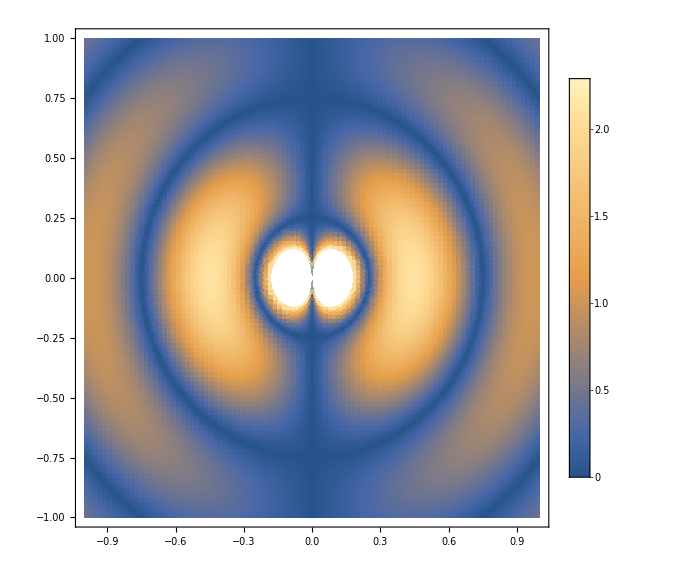

```mathematica
CE[y_,z_, t_]:=Abs[ 1/(√(y^2+z^2))*Sin[ArcCos[z/(√(y^2+z^2))]]* Cos[2π*(t -√(y^2+z^2))]]
optam={ImageSize-> Large,LabelStyle-> Large};
DensityPlot[CE[y,z,0],{y,-1,1},{z,-1,1},Evaluate[optam],PlotPoints->100,PlotLegends->Automatic]
```

```mathematica
Animate[DensityPlot[CE[y,z,t],{y,-1,1},{z,-1,1},Evaluate[optam],PlotPoints->100,PlotLegends->Automatic], {t, 0, 2π,1/24} ]
```

• A partir de uma tabela de imagens, o Mathematica é capaz de produzir arquivos ‘gif’ animados. Se sua tabela tem o nome de ‘tabela’, para produzir um arquivo ‘animado.gif’ que se repita infinitamente utilize a sintaxe Export[“animado.gif”,tabela,”AnimationRepetitions” → ∞].Implemente isso em seu notebook e envie pelos campos mais abaixo o ‘gif’ animado que produzir, juntamente com o próprio notebook.

```mathematica
Export["animado.gif",%,"AnimationRepetitions" -> ∞]
```

animado.gif

## 3.

O calor específico de sólidos cristalinos, na temperatura ambiente, é em geral próximo de 3 k_B, sendo k_B a constante de Boltzmann. (O calor específico a que nos referimos aqui é a capacidade térmica por átomo, e a capacidade térmica, por sua vez, é a razão entre a energia térmica transferida para um corpo e a variação de temperatura associada a essa transferência.) Esse comportamento é bem descrito por um modelo clássico de um sólido como uma coleção de átomos ligados por molas microscópicas. No entanto, efeitos quânticos fazem com que, em baixas temperaturas, o calor específico diminua muito. Dois modelos simples foram propostos nas primeiras décadas do século XX, por Einstein e por Debye, respectivamente, para dar conta dessa diminuição. Os dois modelos são discutidos na disciplina de Mecânica Estatística. Neste problema, você deve buscar ajustar dados experimentais do calor específico do alumínio e do chumbo, utilizando ambos os modelos.

• Utilizando o botão direito do mouse e a opção “Salvar link como” (ou similar), baixe os dados experimentais para o alumínio e o chumbo em função da temperatura (em kelvin). Esses dados correspondem ao calor específico por mol. Após importá-los, para convertê-los para calor específico por átomo, você deve dividir cada medida de calor específico pela “constante universal dos gases”, R = k_B N_A = 8.31 J/K*mol, sendo N_A o número de Avogadro. Assegure-se de dividir por R apenas a segunda coluna de cada tabela de dados. Produza um gráfico mostrando o comportamento do calor específico para ambos os sólidos, que deve se assemelhar ao mostrado na figura abaixo.

(Resposta) Começarei chamando os dados e convertendo a segunda coluna para calor especifico por átomo. Após isso, realizarei o plot.

```mathematica
SetDirectory[NotebookDirectory[]];
Pb = Import["dados_Pb.dat"];
dPb = Transpose[Pb];
TPb = dPb[[1]];
CalorPb =  dPb[[2]]/8.31;
dadoPb = Transpose[{TPb ,CalorPb}];
Al = Import["dados_Al.dat"];
dAl = Transpose[Al];
TAl = dAl[[1]];
CalorAl =  dAl[[2]]/8.31;
dadoAl = Transpose[{TAl ,CalorAl}];
```

```mathematica
grafico = ListPlot[{dadoAl,dadoPb}, PlotLabels->{"Al","Pb"},AxesLabel->{"T(K)","c/k_b"},ImageSize-> Large,LabelStyle-> Large]
```

-Graphics-

• Primeiro faça o ajuste dos dados utilizando o modelo de Einstein. Segundo esse modelo, a energia interna por átomo, dividida por k_B, é dada por: u/k_B = 3/2 ℏω/k_B(Exp[ℏω/k_BT] +1)/(Exp[ℏω/k_BT] -1), em que ℏ é a constante de Planck reduzida e ω é a frequência  dos osciladores de Einstein em um dado material. Utilizando a relação termodinâmica ℏ = k_B = 1 (o que equivale nesse caso a medir frequências em kelvin!), determine o valor de ω que melhor ajusta (por mínimos quadrados) os dados experimentais para cada sólido, usando como palpite inicial para a frequência o valor T^* da temperatura em que o calor específico atinge (aproximadamente) a metade do seu valor de altas temperaturas. (Grosseiramente, podemos dizer que essa temperatura separa os regimes “quântico” e “clássico”.)

(Resposta) Observando no gráfico percebemos que a T^* para cada sólido será calculado medindo com o cursor o valor do calor especifico em 300 K e procurando, no caminho que os dados parecem percorrer, o valor da temperatura para metade desse calor:

```mathematica
estrelaTPb = 20.5;
estrelaTAl = 93.8;
```

O calor específico é dado pela derivada da energia interna pela temperatura, com isso temos a seguinte expressão:

```mathematica
ceinstein[T_]:=D[ 3/2*ω*(Exp[ω/T] +1)/(Exp[ω/T] -1)   ,T]
ajusteeinsteinPb= FindFit[dadoPb, ceinstein[T],{{ω,estrelaTPb}},T]
ajusteeinsteinAl= FindFit[dadoAl, ceinstein[T],{{ω,estrelaTAl}},T]
```

{ω→65.5686}

{ω→276.714}

• Agora faça o ajuste dos dados utilizando o modelo de Debye. Nesse caso, o calor específico é dado por: c = 9 (k_B(T/T_D))^3∫_0^(T_D/T) ⅆη (η^4 ℯ^η)/((ℯ^η - 1)^2), em que T_D é a temperatura de Debye, uma propriedade de cada material. Determine o valor de T_D que melhor ajusta (por mínimos quadrados) os dados experimentais para cada sólido, usando como palpite inicial para T_D o valor correspondente de T^* do item anterior.

```mathematica
cdebye[T_]:= 9 *( T/td)^3*NIntegrate[(x^4*Exp[x])/(Exp[x] - 1)^2,{x,0,td/T}]
ajustedebyePb= FindFit[dadoPb, cdebye[T],{{td,estrelaTPb}},T]
ajustedebyeAl= FindFit[dadoAl, cdebye[T],{{td,estrelaTAl}},T]
```

{td→88.0244}

{td→378.439}

• Por fim, faça um gráfico mostrando os dados experimentais e os ajustes por ambos os modelos. Você deve obter algo semelhante ao mostrado na figura abaixo, de onde se pode notar, observando o caso do alumínio, que ambos os modelos fornecem uma descrição teórica comparável em temperaturas acima de T^*,  mas que o modelo de Debye é muito mais preciso em temperaturas mais baixas.

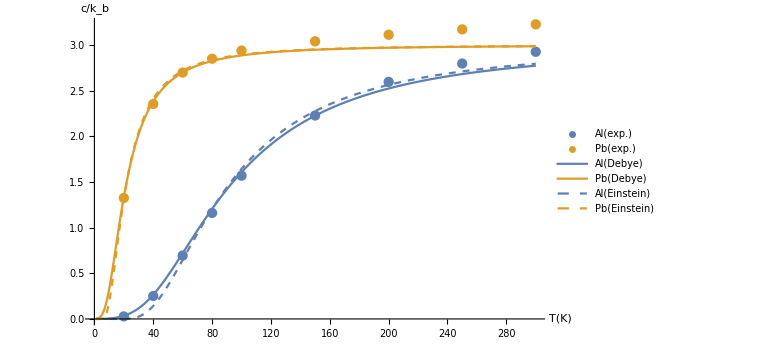

```mathematica
graficoexp = ListPlot[{dadoAl,dadoPb}, PlotLegends->{"Al(exp.)","Pb(exp.)"},AxesLabel->{"T(K)","c/k_b"},ImageSize-> Large,LabelStyle-> Large];
graficoEinstein = Plot[{Evaluate[ceinstein[T]/.ajusteeinsteinAl],Evaluate[ceinstein[T]/.ajusteeinsteinPb]}, {T,1,300}, PlotStyle->{ Dashed}, PlotLegends->{"Al(Einstein)","Pb(Einstein)"},AxesLabel->{"T(K)","c/k_b"},ImageSize-> Large,LabelStyle-> Large, PlotPoints->200];
graficoDebye = Plot[{Evaluate[cdebye[T]/.ajustedebyeAl],Evaluate[cdebye[T]/.ajustedebyePb]}, {T,1,300}, PlotStyle->{ Thick}, PlotLegends->{"Al(Debye)","Pb(Debye)"},AxesLabel->{"T(K)","c/k_b"},ImageSize-> Large,LabelStyle-> Large, PlotPoints->200];
Show[{graficoexp,graficoDebye,graficoEinstein}]
```